```mathematica
cal[nums_List,t_]:=Block[{ops,num=nums,rule,same,filter},ops={Plus,Subtract,Times,Divide};
rule=Thread[num->{x,y,z,w}];
same[a_,b_]:=Block[{p,q},p=a/.rule;
q=b/.rule;ReleaseHold[p]===ReleaseHold[q]];
filter[{op1_,op2_,op3_},{a_,b_,c_,d_}]:=Block[{ans={}},
If[Quiet@op1[op2[op3[a,b],c],d]==t,ans=num,
If[Quiet@op1[op2[a,b],op3[c,d]]==t,ans=num,
If[Quiet@op1[op2[a,op3[b,c]],d]==t,ans=num,
If[Quiet@op1[a,op2[b,op3[c,d]]]==t,ans=num]]]]
ans];
filter@@@Tuples[{Tuples[ops,3],Permutations[num]}]]
data=DeleteDuplicates[Sort/@Permutations[Table[ConstantArray[i,4],{i,1,6}]//Flatten,{4}]];
judge[nums_List,t_]:=If[Last[SortBy[cal[nums,t], Total]]≠{},nums]
f[n_]:=Block[{data,ansdata,result},
data=DeleteDuplicates[Sort/@Permutations[Table[ConstantArray[i,4],{i,1,n}]//Flatten,{4}]];
ansdata[t_]:=ParallelMap[judge[#,t]&,data];
result[t_]:=DeleteCases[ansdata[t],Null]//Length;
Table[result[k],{k,1,100}]//AbsoluteTiming]
```

```mathematica
For[i=2,i≤13,i++,Print[f[i]]]
```

{1.6713,{5,5,5,5,4,4,2,3,2,2,0,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{4.2472,{15,15,15,15,14,14,12,13,12,11,7,11,5,5,7,7,3,8,2,4,5,1,0,6,2,1,4,1,1,4,0,0,1,0,0,4,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{10.2968,{35,35,35,35,34,34,31,33,31,28,22,31,20,20,24,26,16,22,13,21,14,11,7,23,8,6,11,14,4,13,4,15,7,4,5,18,1,2,3,8,0,3,0,4,5,1,1,12,2,1,2,3,0,4,0,3,1,0,0,6,1,1,2,6,1,1,1,2,0,0,0,5,0,0,0,1,0,0,0,3,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0}}

{23.2778,{70,70,68,70,69,69,64,66,65,63,55,62,46,47,58,58,43,48,40,53,40,34,27,53,35,27,32,36,20,41,18,34,20,14,26,38,9,9,12,34,6,16,6,16,27,7,5,29,8,19,6,10,3,13,13,10,3,2,2,28,2,2,8,12,9,3,1,4,3,10,1,14,1,1,12,5,2,3,2,16,5,1,1,6,4,0,1,2,0,9,0,2,0,0,4,9,1,1,1,11}}

{44.6489,{126,126,122,122,125,125,117,119,117,117,107,118,92,95,103,104,81,101,80,97,78,75,61,105,70,68,66,74,49,93,44,73,48,46,60,89,34,37,36,68,23,56,19,40,53,25,15,73,22,42,20,23,13,47,25,32,12,13,9,68,7,8,18,24,17,27,5,12,10,28,5,49,4,6,23,12,7,20,2,28,11,2,1,28,8,2,4,10,1,33,2,6,5,3,9,30,2,2,6,20}}

{80.8095,{206,209,202,195,203,207,199,195,194,191,178,196,167,176,174,170,140,164,143,164,150,135,117,170,126,119,122,145,103,154,92,128,95,95,130,150,76,80,78,124,67,123,61,81,96,58,54,133,77,81,55,55,39,90,59,88,38,38,28,111,25,26,65,52,43,56,21,28,25,76,16,89,15,16,41,27,41,38,12,52,24,13,9,78,20,9,13,25,8,61,29,15,12,8,18,55,6,33,16,32}}

{136.685,{318,328,314,311,311,318,309,309,300,302,274,304,260,282,276,285,229,252,215,264,232,219,195,275,192,193,197,242,168,234,153,225,160,161,203,240,124,136,141,222,124,201,112,151,159,114,107,234,135,145,106,116,80,155,109,180,84,90,67,185,62,75,124,140,84,105,52,74,57,135,43,173,38,42,71,63,70,79,29,126,45,33,23,124,39,24,29,78,22,104,52,39,26,20,33,127,18,62,36,57}}

{212.326,{467,492,470,460,456,463,457,455,453,447,417,444,386,409,414,425,353,405,335,385,354,315,297,404,300,300,332,350,255,337,236,328,266,242,297,375,202,204,232,324,193,285,169,241,278,187,173,340,216,224,186,186,149,277,187,275,159,152,120,276,117,136,238,224,145,176,97,126,123,211,99,293,92,96,137,116,125,143,79,208,143,80,60,203,79,59,77,131,60,206,88,73,65,43,58,196,42,95,107,97}}

{324.806,{663,709,675,662,662,656,646,653,644,647,599,637,554,597,592,606,509,591,496,586,508,474,420,566,431,454,465,504,373,522,350,463,373,364,428,529,300,326,336,496,281,415,248,360,412,299,254,462,308,378,279,284,227,412,290,391,235,247,197,440,192,230,338,331,237,282,159,213,203,368,169,421,158,179,225,198,203,237,145,374,226,158,116,308,157,130,135,223,117,358,153,141,118,113,120,292,85,170,178,227}}

{460.402,{900,980,926,906,898,894,873,879,878,879,841,870,779,812,799,818,702,795,691,794,714,712,606,756,602,611,640,664,543,702,504,641,583,509,592,709,431,456,479,670,403,554,387,560,562,414,364,611,429,508,404,404,341,556,464,539,340,341,313,590,292,323,460,457,353,460,266,312,310,508,268,566,241,271,342,310,364,348,238,513,339,235,204,440,254,212,225,400,201,491,254,223,193,189,206,416,158,261,334,339}}

{8942.69,{1215,1339,1265,1235,1215,1230,1179,1190,1183,1185,1136,1190,1064,1123,1093,1108,944,1088,918,1066,976,964,830,1068,809,820,853,909,709,944,660,868,798,691,776,1004,593,626,650,896,531,769,528,775,736,551,498,889,572,657,542,574,449,750,614,721,477,468,431,862,401,444,614,605,480,652,369,470,435,658,368,832,347,375,469,459,491,510,324,687,461,340,302,686,360,307,337,564,290,660,356,355,296,282,308,645,248,384,462,494}}

$Aborted

```mathematica
f[12]
```

{676.135,{1215,1339,1265,1235,1215,1230,1179,1190,1183,1185,1136,1190,1064,1123,1093,1108,944,1088,918,1066,976,964,830,1068,809,820,853,909,709,944,660,868,798,691,776,1004,593,626,650,896,531,769,528,775,736,551,498,889,572,657,542,574,449,750,614,721,477,468,431,862,401,444,614,605,480,652,369,470,435,658,368,832,347,375,469,459,491,510,324,687,461,340,302,686,360,307,337,564,290,660,356,355,296,282,308,645,248,384,462,494}}

```mathematica
f[13]
```

{930.417,{1565,1757,1644,1601,1563,1577,1527,1519,1526,1528,1470,1535,1414,1448,1438,1423,1240,1393,1197,1370,1252,1240,1108,1361,1074,1159,1134,1169,942,1190,890,1105,1033,892,1017,1266,821,830,948,1152,723,997,718,980,950,726,677,1137,762,843,725,847,633,928,795,915,647,613,590,1106,564,586,789,800,733,834,532,621,587,837,500,1053,495,497,634,613,687,769,456,876,598,453,447,873,507,424,466,724,395,864,569,497,426,388,437,829,373,519,611,654}}

```mathematica
data={{5,5,5,5,4,4,2,3,2,2,0,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{15,15,15,15,14,14,12,13,12,11,7,11,5,5,7,7,3,8,2,4,5,1,0,6,2,1,4,1,1,4,0,0,1,0,0,4,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{35,35,35,35,34,34,31,33,31,28,22,31,20,20,24,26,16,22,13,21,14,11,7,23,8,6,11,14,4,13,4,15,7,4,5,18,1,2,3,8,0,3,0,4,5,1,1,12,2,1,2,3,0,4,0,3,1,0,0,6,1,1,2,6,1,1,1,2,0,0,0,5,0,0,0,1,0,0,0,3,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0},
{70,70,68,70,69,69,64,66,65,63,55,62,46,47,58,58,43,48,40,53,40,34,27,53,35,27,32,36,20,41,18,34,20,14,26,38,9,9,12,34,6,16,6,16,27,7,5,29,8,19,6,10,3,13,13,10,3,2,2,28,2,2,8,12,9,3,1,4,3,10,1,14,1,1,12,5,2,3,2,16,5,1,1,6,4,0,1,2,0,9,0,2,0,0,4,9,1,1,1,11},
{126,126,122,122,125,125,117,119,117,117,107,118,92,95,103,104,81,101,80,97,78,75,61,105,70,68,66,74,49,93,44,73,48,46,60,89,34,37,36,68,23,56,19,40,53,25,15,73,22,42,20,23,13,47,25,32,12,13,9,68,7,8,18,24,17,27,5,12,10,28,5,49,4,6,23,12,7,20,2,28,11,2,1,28,8,2,4,10,1,33,2,6,5,3,9,30,2,2,6,20},
{206,209,202,195,203,207,199,195,194,191,178,196,167,176,174,170,140,164,143,164,150,135,117,170,126,119,122,145,103,154,92,128,95,95,130,150,76,80,78,124,67,123,61,81,96,58,54,133,77,81,55,55,39,90,59,88,38,38,28,111,25,26,65,52,43,56,21,28,25,76,16,89,15,16,41,27,41,38,12,52,24,13,9,78,20,9,13,25,8,61,29,15,12,8,18,55,6,33,16,32},
{318,328,314,311,311,318,309,309,300,302,274,304,260,282,276,285,229,252,215,264,232,219,195,275,192,193,197,242,168,234,153,225,160,161,203,240,124,136,141,222,124,201,112,151,159,114,107,234,135,145,106,116,80,155,109,180,84,90,67,185,62,75,124,140,84,105,52,74,57,135,43,173,38,42,71,63,70,79,29,126,45,33,23,124,39,24,29,78,22,104,52,39,26,20,33,127,18,62,36,57},
{467,492,470,460,456,463,457,455,453,447,417,444,386,409,414,425,353,405,335,385,354,315,297,404,300,300,332,350,255,337,236,328,266,242,297,375,202,204,232,324,193,285,169,241,278,187,173,340,216,224,186,186,149,277,187,275,159,152,120,276,117,136,238,224,145,176,97,126,123,211,99,293,92,96,137,116,125,143,79,208,143,80,60,203,79,59,77,131,60,206,88,73,65,43,58,196,42,95,107,97},
{663,709,675,662,662,656,646,653,644,647,599,637,554,597,592,606,509,591,496,586,508,474,420,566,431,454,465,504,373,522,350,463,373,364,428,529,300,326,336,496,281,415,248,360,412,299,254,462,308,378,279,284,227,412,290,391,235,247,197,440,192,230,338,331,237,282,159,213,203,368,169,421,158,179,225,198,203,237,145,374,226,158,116,308,157,130,135,223,117,358,153,141,118,113,120,292,85,170,178,227},
{900,980,926,906,898,894,873,879,878,879,841,870,779,812,799,818,702,795,691,794,714,712,606,756,602,611,640,664,543,702,504,641,583,509,592,709,431,456,479,670,403,554,387,560,562,414,364,611,429,508,404,404,341,556,464,539,340,341,313,590,292,323,460,457,353,460,266,312,310,508,268,566,241,271,342,310,364,348,238,513,339,235,204,440,254,212,225,400,201,491,254,223,193,189,206,416,158,261,334,339},
{1215,1339,1265,1235,1215,1230,1179,1190,1183,1185,1136,1190,1064,1123,1093,1108,944,1088,918,1066,976,964,830,1068,809,820,853,909,709,944,660,868,798,691,776,1004,593,626,650,896,531,769,528,775,736,551,498,889,572,657,542,574,449,750,614,721,477,468,431,862,401,444,614,605,480,652,369,470,435,658,368,832,347,375,469,459,491,510,324,687,461,340,302,686,360,307,337,564,290,660,356,355,296,282,308,645,248,384,462,494},
{1565,1757,1644,1601,1563,1577,1527,1519,1526,1528,1470,1535,1414,1448,1438,1423,1240,1393,1197,1370,1252,1240,1108,1361,1074,1159,1134,1169,942,1190,890,1105,1033,892,1017,1266,821,830,948,1152,723,997,718,980,950,726,677,1137,762,843,725,847,633,928,795,915,647,613,590,1106,564,586,789,800,733,834,532,621,587,837,500,1053,495,497,634,613,687,769,456,876,598,453,447,873,507,424,466,724,395,864,569,497,426,388,437,829,373,519,611,654}};
```

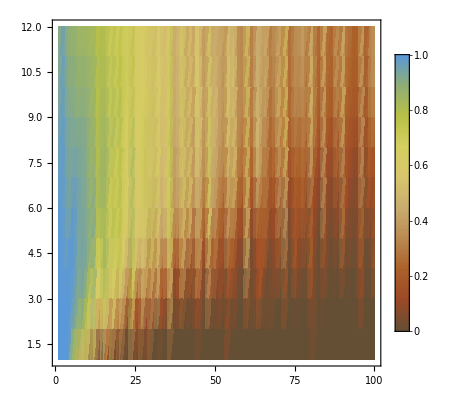
{-Graphics3D-,-Graphics-}

```mathematica
dataRatio=Divide[dataList,Binomial[#+3,4]&/@Range[2,13]]//N;
{ListPlot3D[dataRatio,Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"],
ListDensityPlot[dataRatio,ColorFunction->"SouthwestColors",PlotLegends->Automatic]}
```

```mathematica
list2={5,5,5,5,4,4,2,3,2,2,0,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}/5 ;
list3={15,15,15,15,14,14,12,13,12,11,7,11,5,5,7,7,3,8,2,4,5,1,0,6,2,1,4,1,1,4,0,0,1,0,0,4,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} /15;
list4={35,35,35,35,34,34,31,33,31,28,22,31,20,20,24,26,16,22,13,21,14,11,7,23,8,6,11,14,4,13,4,15,7,4,5,18,1,2,3,8,0,3,0,4,5,1,1,12,2,1,2,3,0,4,0,3,1,0,0,6,1,1,2,6,1,1,1,2,0,0,0,5,0,0,0,1,0,0,0,3,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0} /35;
list10={663,709,675,662,662,656,646,653,644,647,599,637,554,597,592,606,509,591,496,586,508,474,420,566,431,454,465,504,373,522,350,463,373,364,428,529,300,326,336,496,281,415,248,360,412,299,254,462,308,378,279,284,227,412,290,391,235,247,197,440,192,230,338,331,237,282,159,213,203,368,169,421,158,179,225,198,203,237,145,374,226,158,116,308,157,130,135,223,117,358,153,141,118,113,120,292,85,170,178,227}/715; list13={1565,1757,1644,1601,1563,1577,1527,1519,1526,1528,1470,1535,1414,1448,1438,1423,1240,1393,1197,1370,1252,1240,1108,1361,1074,1159,1134,1169,942,1190,890,1105,1033,892,1017,1266,821,830,948,1152,723,997,718,980,950,726,677,1137,762,843,725,847,633,928,795,915,647,613,590,1106,564,586,789,800,733,834,532,621,587,837,500,1053,495,497,634,613,687,769,456,876,598,453,447,873,507,424,466,724,395,864,569,497,426,388,437,829,373,519,611,654}/1820;
{ListLinePlot[{list2,list3,list4,list10,list13},PlotTheme->"Detailed",PlotLegends->{"list2","list3","list4","list10","list13"}],
ListLinePlot[{list10,list13},PlotTheme->"Business",DataRange->{0,36},PlotRange->{0.1,1.0},PlotLegends->{"list10","list13"}]}
```

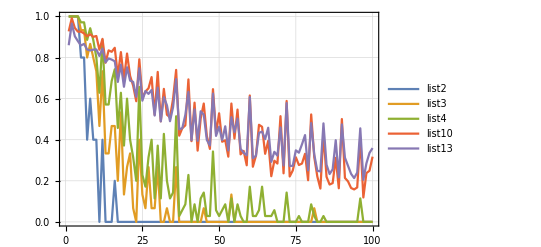
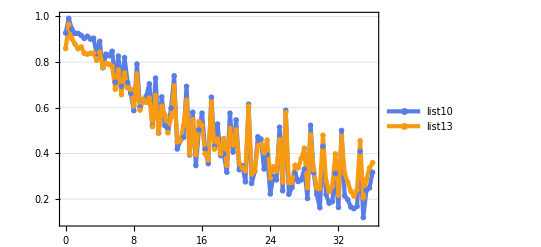
```mathematica
-Graphics-      -Graphics-
-Graphics3D-                     -Graphics-
```

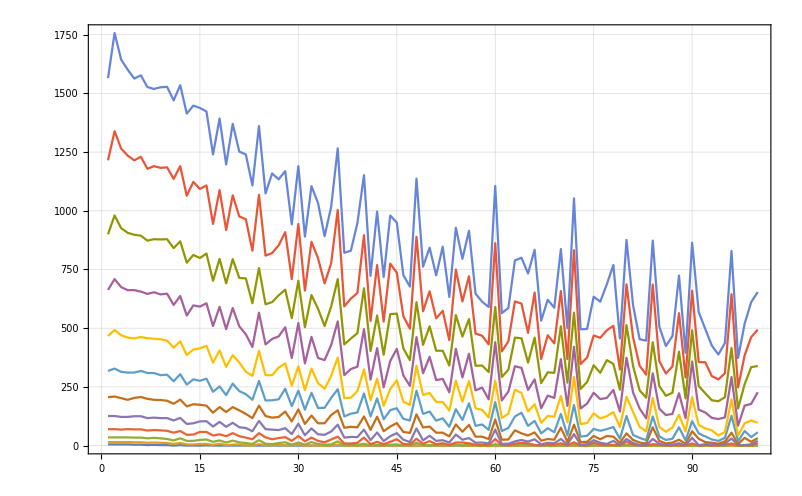

```mathematica
ListLinePlot[dataList,PlotTheme->"Detailed"]
ListLinePlot[dataRatio,PlotTheme->"Detailed"]
```

```mathematica
data=ParallelTable[Length@cal24[4,i,j],{j,100},{i,13},Method->"CoarsestGrained"];//TT
```

CPU Time:  1.59375

All Time:  121.357

```mathematica
data
```

{{18,126,366,772,1333,2174,3126,4436,5957,7811,9757,12450,15005},{14,110,318,713,1177,1978,2764,3974,5209,6923,8467,10910,12896},{6,77,266,586,1020,1727,2448,3415,4692,6036,7436,9632,11447},{2,55,205,550,976,1641,2312,3429,4483,5890,7187,9373,11048},{0,24,134,365,798,1366,2022,2859,3850,5225,6487,8176,9772},{0,29,136,368,709,1425,2112,3059,4136,5451,6671,8829,10386},{0,5,67,215,475,910,1657,2497,3446,4532,5701,7239,8737},{0,13,68,257,506,949,1511,2607,3622,4886,6062,7896,9385},{0,3,59,159,383,758,1219,1918,3166,4341,5568,7199,8671},{0,4,39,149,377,743,1163,1838,2675,4236,5533,7211,8685},{0,0,20,79,220,464,819,1292,1957,2897,4473,6014,7516},{0,4,47,173,331,725,1130,1794,2558,3551,4697,7039,8766},{0,0,9,59,166,321,643,1038,1566,2245,3114,4418,6510},{0,0,11,72,179,390,762,1249,1777,2581,3400,4658,6054},{0,0,20,74,220,426,692,1094,1710,2459,3239,4405,5615},{0,3,12,96,201,392,623,1188,1711,2426,3185,4362,5447},{0,0,3,30,104,204,395,645,1070,1577,2213,3000,3945},{0,0,18,64,155,411,637,979,1620,2338,3041,4224,5213},{0,0,2,22,84,173,346,534,849,1315,1923,2595,3437},{0,0,7,63,193,356,552,935,1282,2084,2771,3779,4695},{0,0,7,29,104,234,483,710,1120,1509,2140,2955,3787},{0,0,1,18,70,183,334,574,817,1254,1970,2749,3552},{0,0,0,9,55,122,252,421,665,930,1342,1930,2679},{0,0,11,62,146,363,557,978,1389,1883,2397,3621,4505},{0,0,2,11,96,182,326,488,745,1131,1547,2009,2751},{0,0,1,9,50,144,259,445,663,1028,1381,1877,2793},{0,0,5,15,59,152,285,448,871,1161,1561,2097,2710},{0,0,1,27,74,170,390,676,926,1321,1689,2340,2917},{0,0,1,4,33,90,188,316,492,691,1044,1357,1829},{0,0,4,19,98,278,439,665,980,1580,2002,2753,3332},{0,0,0,4,21,80,178,289,446,652,970,1260,1711},{0,0,0,27,60,143,261,592,817,1138,1491,2073,2553},{0,0,1,7,28,98,199,336,588,796,1279,1750,2247},{0,0,0,4,18,80,167,301,467,740,998,1355,1740},{0,0,0,5,49,118,300,453,648,951,1292,1638,2120},{0,0,6,25,61,216,363,605,1017,1371,1754,2649,3209},{0,0,0,1,12,48,135,225,372,548,762,1029,1451},{0,0,0,2,11,53,128,253,382,629,883,1187,1523},{0,0,0,4,16,59,147,258,468,659,924,1257,1890},{0,0,0,12,66,143,257,540,767,1280,1625,2154,2649},{0,0,0,0,9,36,107,202,339,483,718,921,1236},{0,0,0,6,25,118,306,485,710,1005,1305,1855,2284},{0,0,0,0,7,23,102,195,303,436,660,874,1215},{0,0,0,5,20,59,138,288,457,681,1127,1572,1923},{0,0,1,5,39,84,170,293,620,927,1226,1607,2001},{0,0,0,1,7,31,87,180,296,511,715,959,1249},{0,0,0,1,5,17,77,157,271,392,594,819,1089},{0,0,0,17,38,130,242,531,770,1054,1348,2132,2621},{0,0,0,2,8,24,147,253,403,566,782,1007,1358},{0,0,0,1,29,63,132,261,397,790,1034,1327,1674},{0,0,0,2,7,25,74,148,312,464,699,961,1238},{0,0,0,4,12,31,90,214,341,539,746,1101,1685},{0,0,0,0,3,13,52,119,216,340,530,697,1003},{0,0,2,4,14,78,143,257,557,806,1063,1502,1832},{0,0,0,0,14,37,92,185,316,523,908,1160,1491},{0,0,0,4,15,43,162,391,571,803,1082,1463,1798},{0,0,0,1,4,15,50,131,273,406,576,825,1116},{0,0,0,0,2,13,38,114,211,368,515,721,958},{0,0,0,0,2,10,33,86,169,288,480,646,883},{0,0,0,6,36,109,183,342,540,971,1293,2006,2441},{0,0,0,1,2,9,32,83,172,276,459,638,899},{0,0,0,1,2,10,31,104,191,338,477,678,896},{0,0,0,2,9,23,105,200,463,638,867,1155,1484},{0,0,0,8,15,32,62,255,401,606,810,1104,1401},{0,0,0,1,10,20,56,124,243,402,601,817,1311},{0,0,0,1,3,42,81,159,286,470,858,1244,1556},{0,0,0,1,1,5,26,66,137,229,387,556,803},{0,0,0,2,5,14,36,105,208,351,505,787,1053},{0,0,0,0,3,10,27,68,172,279,436,639,883},{0,0,0,0,11,30,113,204,333,672,913,1194,1496},{0,0,0,0,1,5,18,55,138,241,393,541,736},{0,0,0,5,16,76,127,293,586,833,1094,1764,2165},{0,0,0,0,1,4,17,44,130,235,358,503,742},{0,0,0,0,1,6,19,49,119,246,389,544,719},{0,0,0,0,14,27,48,89,206,362,538,773,1039},{0,0,0,1,5,12,29,73,150,282,438,681,922},{0,0,0,0,2,8,60,103,192,307,624,836,1142},{0,0,0,0,3,23,55,108,209,351,514,815,1335},{0,0,0,0,2,2,15,34,106,193,328,454,654},{0,0,0,3,20,37,67,201,331,688,930,1255,1564},{0,0,1,1,5,11,26,50,244,376,558,751,968},{0,0,0,0,1,2,13,34,96,219,330,501,667},{0,0,0,0,1,1,10,29,76,150,282,413,630},{0,0,0,1,7,34,118,197,323,500,712,1252,1587},{0,0,0,0,5,9,24,50,112,233,375,532,793},{0,0,0,0,0,2,11,30,76,174,286,425,596},{0,0,0,0,1,4,14,30,89,172,296,461,639},{0,0,0,0,2,10,28,115,191,335,680,966,1233},{0,0,0,0,0,1,8,23,71,155,279,414,569},{0,0,0,0,11,44,77,135,328,654,891,1234,1581},{0,0,0,0,0,2,39,71,122,235,398,553,974},{0,0,0,0,2,6,15,44,81,174,298,511,711},{0,0,0,0,0,5,12,26,69,139,244,397,590},{0,0,0,0,0,3,8,23,50,139,242,369,526},{0,0,0,0,4,9,18,35,70,176,308,455,653},{0,0,0,4,9,37,63,185,281,433,616,1124,1421},{0,0,0,0,1,2,6,20,48,109,211,328,522},{0,0,0,0,1,2,43,79,124,243,377,560,752},{0,0,0,0,1,7,18,42,155,263,567,778,1010},{0,0,0,0,14,24,40,73,119,369,546,808,1053}}

```mathematica
Transpose@data//MatrixForm
```

(18 | 14 | 6 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
126 | 110 | 77 | 55 | 24 | 29 | 5 | 13 | 3 | 4 | 0 | 4 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
366 | 318 | 266 | 205 | 134 | 136 | 67 | 68 | 59 | 39 | 20 | 47 | 9 | 11 | 20 | 12 | 3 | 18 | 2 | 7 | 7 | 1 | 0 | 11 | 2 | 1 | 5 | 1 | 1 | 4 | 0 | 0 | 1 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
772 | 713 | 586 | 550 | 365 | 368 | 215 | 257 | 159 | 149 | 79 | 173 | 59 | 72 | 74 | 96 | 30 | 64 | 22 | 63 | 29 | 18 | 9 | 62 | 11 | 9 | 15 | 27 | 4 | 19 | 4 | 27 | 7 | 4 | 5 | 25 | 1 | 2 | 4 | 12 | 0 | 6 | 0 | 5 | 5 | 1 | 1 | 17 | 2 | 1 | 2 | 4 | 0 | 4 | 0 | 4 | 1 | 0 | 0 | 6 | 1 | 1 | 2 | 8 | 1 | 1 | 1 | 2 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0
1333 | 1177 | 1020 | 976 | 798 | 709 | 475 | 506 | 383 | 377 | 220 | 331 | 166 | 179 | 220 | 201 | 104 | 155 | 84 | 193 | 104 | 70 | 55 | 146 | 96 | 50 | 59 | 74 | 33 | 98 | 21 | 60 | 28 | 18 | 49 | 61 | 12 | 11 | 16 | 66 | 9 | 25 | 7 | 20 | 39 | 7 | 5 | 38 | 8 | 29 | 7 | 12 | 3 | 14 | 14 | 15 | 4 | 2 | 2 | 36 | 2 | 2 | 9 | 15 | 10 | 3 | 1 | 5 | 3 | 11 | 1 | 16 | 1 | 1 | 14 | 5 | 2 | 3 | 2 | 20 | 5 | 1 | 1 | 7 | 5 | 0 | 1 | 2 | 0 | 11 | 0 | 2 | 0 | 0 | 4 | 9 | 1 | 1 | 1 | 14
2174 | 1978 | 1727 | 1641 | 1366 | 1425 | 910 | 949 | 758 | 743 | 464 | 725 | 321 | 390 | 426 | 392 | 204 | 411 | 173 | 356 | 234 | 183 | 122 | 363 | 182 | 144 | 152 | 170 | 90 | 278 | 80 | 143 | 98 | 80 | 118 | 216 | 48 | 53 | 59 | 143 | 36 | 118 | 23 | 59 | 84 | 31 | 17 | 130 | 24 | 63 | 25 | 31 | 13 | 78 | 37 | 43 | 15 | 13 | 10 | 109 | 9 | 10 | 23 | 32 | 20 | 42 | 5 | 14 | 10 | 30 | 5 | 76 | 4 | 6 | 27 | 12 | 8 | 23 | 2 | 37 | 11 | 2 | 1 | 34 | 9 | 2 | 4 | 10 | 1 | 44 | 2 | 6 | 5 | 3 | 9 | 37 | 2 | 2 | 7 | 24
3126 | 2764 | 2448 | 2312 | 2022 | 2112 | 1657 | 1511 | 1219 | 1163 | 819 | 1130 | 643 | 762 | 692 | 623 | 395 | 637 | 346 | 552 | 483 | 334 | 252 | 557 | 326 | 259 | 285 | 390 | 188 | 439 | 178 | 261 | 199 | 167 | 300 | 363 | 135 | 128 | 147 | 257 | 107 | 306 | 102 | 138 | 170 | 87 | 77 | 242 | 147 | 132 | 74 | 90 | 52 | 143 | 92 | 162 | 50 | 38 | 33 | 183 | 32 | 31 | 105 | 62 | 56 | 81 | 26 | 36 | 27 | 113 | 18 | 127 | 17 | 19 | 48 | 29 | 60 | 55 | 15 | 67 | 26 | 13 | 10 | 118 | 24 | 11 | 14 | 28 | 8 | 77 | 39 | 15 | 12 | 8 | 18 | 63 | 6 | 43 | 18 | 40
4436 | 3974 | 3415 | 3429 | 2859 | 3059 | 2497 | 2607 | 1918 | 1838 | 1292 | 1794 | 1038 | 1249 | 1094 | 1188 | 645 | 979 | 534 | 935 | 710 | 574 | 421 | 978 | 488 | 445 | 448 | 676 | 316 | 665 | 289 | 592 | 336 | 301 | 453 | 605 | 225 | 253 | 258 | 540 | 202 | 485 | 195 | 288 | 293 | 180 | 157 | 531 | 253 | 261 | 148 | 214 | 119 | 257 | 185 | 391 | 131 | 114 | 86 | 342 | 83 | 104 | 200 | 255 | 124 | 159 | 66 | 105 | 68 | 204 | 55 | 293 | 44 | 49 | 89 | 73 | 103 | 108 | 34 | 201 | 50 | 34 | 29 | 197 | 50 | 30 | 30 | 115 | 23 | 135 | 71 | 44 | 26 | 23 | 35 | 185 | 20 | 79 | 42 | 73
5957 | 5209 | 4692 | 4483 | 3850 | 4136 | 3446 | 3622 | 3166 | 2675 | 1957 | 2558 | 1566 | 1777 | 1710 | 1711 | 1070 | 1620 | 849 | 1282 | 1120 | 817 | 665 | 1389 | 745 | 663 | 871 | 926 | 492 | 980 | 446 | 817 | 588 | 467 | 648 | 1017 | 372 | 382 | 468 | 767 | 339 | 710 | 303 | 457 | 620 | 296 | 271 | 770 | 403 | 397 | 312 | 341 | 216 | 557 | 316 | 571 | 273 | 211 | 169 | 540 | 172 | 191 | 463 | 401 | 243 | 286 | 137 | 208 | 172 | 333 | 138 | 586 | 130 | 119 | 206 | 150 | 192 | 209 | 106 | 331 | 244 | 96 | 76 | 323 | 112 | 76 | 89 | 191 | 71 | 328 | 122 | 81 | 69 | 50 | 70 | 281 | 48 | 124 | 155 | 119
7811 | 6923 | 6036 | 5890 | 5225 | 5451 | 4532 | 4886 | 4341 | 4236 | 2897 | 3551 | 2245 | 2581 | 2459 | 2426 | 1577 | 2338 | 1315 | 2084 | 1509 | 1254 | 930 | 1883 | 1131 | 1028 | 1161 | 1321 | 691 | 1580 | 652 | 1138 | 796 | 740 | 951 | 1371 | 548 | 629 | 659 | 1280 | 483 | 1005 | 436 | 681 | 927 | 511 | 392 | 1054 | 566 | 790 | 464 | 539 | 340 | 806 | 523 | 803 | 406 | 368 | 288 | 971 | 276 | 338 | 638 | 606 | 402 | 470 | 229 | 351 | 279 | 672 | 241 | 833 | 235 | 246 | 362 | 282 | 307 | 351 | 193 | 688 | 376 | 219 | 150 | 500 | 233 | 174 | 172 | 335 | 155 | 654 | 235 | 174 | 139 | 139 | 176 | 433 | 109 | 243 | 263 | 369
9757 | 8467 | 7436 | 7187 | 6487 | 6671 | 5701 | 6062 | 5568 | 5533 | 4473 | 4697 | 3114 | 3400 | 3239 | 3185 | 2213 | 3041 | 1923 | 2771 | 2140 | 1970 | 1342 | 2397 | 1547 | 1381 | 1561 | 1689 | 1044 | 2002 | 970 | 1491 | 1279 | 998 | 1292 | 1754 | 762 | 883 | 924 | 1625 | 718 | 1305 | 660 | 1127 | 1226 | 715 | 594 | 1348 | 782 | 1034 | 699 | 746 | 530 | 1063 | 908 | 1082 | 576 | 515 | 480 | 1293 | 459 | 477 | 867 | 810 | 601 | 858 | 387 | 505 | 436 | 913 | 393 | 1094 | 358 | 389 | 538 | 438 | 624 | 514 | 328 | 930 | 558 | 330 | 282 | 712 | 375 | 286 | 296 | 680 | 279 | 891 | 398 | 298 | 244 | 242 | 308 | 616 | 211 | 377 | 567 | 546
12450 | 10910 | 9632 | 9373 | 8176 | 8829 | 7239 | 7896 | 7199 | 7211 | 6014 | 7039 | 4418 | 4658 | 4405 | 4362 | 3000 | 4224 | 2595 | 3779 | 2955 | 2749 | 1930 | 3621 | 2009 | 1877 | 2097 | 2340 | 1357 | 2753 | 1260 | 2073 | 1750 | 1355 | 1638 | 2649 | 1029 | 1187 | 1257 | 2154 | 921 | 1855 | 874 | 1572 | 1607 | 959 | 819 | 2132 | 1007 | 1327 | 961 | 1101 | 697 | 1502 | 1160 | 1463 | 825 | 721 | 646 | 2006 | 638 | 678 | 1155 | 1104 | 817 | 1244 | 556 | 787 | 639 | 1194 | 541 | 1764 | 503 | 544 | 773 | 681 | 836 | 815 | 454 | 1255 | 751 | 501 | 413 | 1252 | 532 | 425 | 461 | 966 | 414 | 1234 | 553 | 511 | 397 | 369 | 455 | 1124 | 328 | 560 | 778 | 808
15005 | 12896 | 11447 | 11048 | 9772 | 10386 | 8737 | 9385 | 8671 | 8685 | 7516 | 8766 | 6510 | 6054 | 5615 | 5447 | 3945 | 5213 | 3437 | 4695 | 3787 | 3552 | 2679 | 4505 | 2751 | 2793 | 2710 | 2917 | 1829 | 3332 | 1711 | 2553 | 2247 | 1740 | 2120 | 3209 | 1451 | 1523 | 1890 | 2649 | 1236 | 2284 | 1215 | 1923 | 2001 | 1249 | 1089 | 2621 | 1358 | 1674 | 1238 | 1685 | 1003 | 1832 | 1491 | 1798 | 1116 | 958 | 883 | 2441 | 899 | 896 | 1484 | 1401 | 1311 | 1556 | 803 | 1053 | 883 | 1496 | 736 | 2165 | 742 | 719 | 1039 | 922 | 1142 | 1335 | 654 | 1564 | 968 | 667 | 630 | 1587 | 793 | 596 | 639 | 1233 | 569 | 1581 | 974 | 711 | 590 | 526 | 653 | 1421 | 522 | 752 | 1010 | 1053)

```mathematica
par[num_]:=par[num]=Evaluate@DeleteDuplicatesBy[
Groupings[Permutations[Slot/@Range[num]],
{Plus->2,Subtract->2,Times->2,Divide->2},
Factor@*HoldForm],ReleaseHold
]&

cal24[num_Integer,range_Integer: 13,target_Integer: 24]:=Module[
{cf,displayf,list,x},
cf=With[{expr=If[Times@@Cases[#,Power[x_,-1]:>x,∞]≠0,#,-1.]&/@ReleaseHold[par[num]@@Quiet@Table[x[[i]],{i,num}]]},Compile[{{x,_Real,1}},expr,RuntimeAttributes->{Listable}]];
displayf=Map[InputForm,Thread[par[num]],{3}];
list=(#-Range[0,num-1]&/@Subsets[Range[range+num-1],{num}]);
Select[displayf[[#2]]@@list[[#1]]&@@@Position[Round[cf@list-target],0,{-1}]//DeleteDuplicates,ReleaseHold[#]==InputForm[target]&]]
```